```mathematica
g17=Import["http://www.federalreserve.gov/datadownload/Output.aspx?rel=G17&series=809009461b1cba2fd5b4cf5557d9d663&lastObs=100&from=&to=&filetype=csv&label=include&layout=seriesrow"];
date1=Take[DateList[DateString[Take[Extract[g17,{1}],{-100}]]],2];
industrialproduction=Take[Extract[g17,{2}],-100];
utilization=Take[Extract[g17,{12}],-100];
DateListPlot[Tooltip[industrialproduction],date1]
DateListPlot[Tooltip[utilization],date1]
```

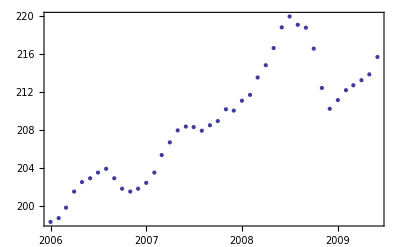

```mathematica
cpi=Import["ftp://ftp.bls.gov/pub/special.requests/cpi/cpiai.txt","Table"];
cpi1=Take[Extract[cpi,-1],{2,Length[Extract[cpi,-1]]}];
cpi2=Take[Extract[cpi,-2],{2,13}];
cpi3=Take[Extract[cpi,-3],{2,13}];
cpi4=Take[Extract[cpi,-4],{2,13}];
cpisample=Join[cpi4,cpi3,cpi2,cpi1];
date2=Take[DateList[DateString[Take[Extract[cpi,-4],1]]],2];
DateListPlot[Tooltip[cpisample],date2]
```